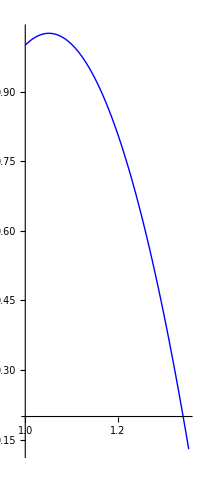

```mathematica
g=9.8; (*grav. constant*)
θ=45*π/180;
v=1;
x0=1;
y0=1;
vx0=v Cos[θ];
vy0=v Sin[θ];
vt=50;

ode1={x''[t] == (-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2], y''[t] == -g (1 + (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]), x[0]==x0, x'[0]==vx0, y[0]==y0,y'[0]==vy0 };
sol=NDSolve[ode1,{x,y},{t,0,20}];
ParametricPlot[{x[t],y[t]}/.sol,{t,0,.5},PlotStyle-> RGBColor[0,0,1],PlotRange-> All]
```

```mathematica
;
```

```mathematica
Manipulate[
g=9.8;
x0=0;
vx0=v Cos[θ];
vy0=v Sin[θ];
Module[
{result = NDSolve[{x''[t] == (-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2], y''[t] == -g (1 + (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]), x[0]==x0, x'[0]==vx0, y[0]==y0,y'[0]==vy0 },{x,y}, {t, 0,50}]},
ParametricPlot[{x[t],y[t]}/.result,{t,0,tmax},PlotStyle-> {{Blue},{Dashed,Red}},PlotRange-> All,AxesLabel->{"x (m)","y (m)"},PlotRange->{{0,8000},{-10,500}},ImageSize->{500,300}]],
{{v,30,"initial velocity (m/s)"},0,500.,Appearance->"Labeled"},{{θ,50*Pi/180,"initial angle (rad)"},0.,π/2,Appearance->"Labeled"},
{{vt,100,"terminal velocity(m/s)"},0,500.,Appearance->"Labeled"},
{{tmax,1.1,"time step(s)"},0,20.,Appearance->"Labeled"},{{y0,1,"initial height (m)"},0,5.,Appearance->"Labeled"}]
```